## Multi-type BP fitting

Relations between the mean, and covariance to the pgf

### Setting up BGW processes

From the paper, recreate the results

```mathematica
qn[q1_,n_,α_]:=q1 (1-α)^(n-1)
pn[q1_,n_,α_]:=1-qn[q1,n,α]

p[y_,n_,u_]:=Binomial[u,y] (pn[q1,n,α])^y*(qn[q1,n,α])^(u-y)
```

```mathematica
p[y,n,u]
```

(1-q1 (1-α)^(-1+n))^y (q1 (1-α)^(-1+n))^(u-y) Binomial[u,y]

```mathematica
p[y,2,u]
```

(1-q1 (1-α))^y (q1 (1-α))^(u-y) Binomial[u,y]

```mathematica
h1[s1_,s2_,s3_,s4_,s5_]:=p[0,1,2]+p[1,1,2]s1*s2*s5+p[2,1,2] s1^2*s3*s5^2;
h2[s1_,s2_,s3_,s4_,s5_]:=p[0,2,1]+p[1,2,1]s1*s4*s5;
h3[s1_,s2_,s3_,s4_]:=1;
h4[s1_,s2_,s3_,s4_]:=1;
h5[s5_]:=s5;
probRule ={s1->0,s2->0,s3->0,s4->0}
expRule ={s1->1,s2->1,s3->1,s4->1}
p[0,1,2]
```

{s1→0,s2→0,s3→0,s4→0}

{s1→1,s2→1,s3→1,s4→1}

q1^2

```mathematica
p[0,2,1]
```

q1 (1-α)

```mathematica
p[1,2,1]
```

1-q1 (1-α)

```mathematica
h1[s1,s2,s3,s4,s5]
```

q1^2+2 (1-q1) q1 s1 s2 s5+(1-q1)^2 s1^2 s3 s5^2

```mathematica
h2[s1,s2,s3,s4,s5]
```

s1 s4 s5 (1-q1 (1-α))+q1 (1-α)

### Dist after two generation

```mathematica
twoGen=h1[h1[s1,s2,s3,s4,s5],h2[s1,s2,s3,s4,s5],h3[s1,s2,s3,s4],h4[s1,s2,s3,s4],h5[s5]]
```

q1^2+(1-q1)^2 s5^2 (q1^2+2 (1-q1) q1 s1 s2 s5+(1-q1)^2 s1^2 s3 s5^2)^2+2 (1-q1) q1 s5 (q1^2+2 (1-q1) q1 s1 s2 s5+(1-q1)^2 s1^2 s3 s5^2) (s1 s4 s5 (1-q1 (1-α))+q1 (1-α))

```mathematica
res=Table[{i,D[twoGen,{s5,i}]/(i!)},{i,0,10}]/.{s1->1,s2->1,s3->1,s4->1,s5->0}/.{q1->0.7,α->0.0}
```

{{0,0.49},{1,0.14406},{2,0.206829},{3,0.116424},{4,0.035154},{5,0.006804},{6,0.000729},{7,0},{8,0},{9,0},{10,0}}

```mathematica
res//TableForm
```

0 | 0.49
1 | 0.14406
2 | 0.206829
3 | 0.116424
4 | 0.035154
5 | 0.006804
6 | 0.000729
7 | 0
8 | 0
9 | 0
10 | 0

```mathematica
Total[res,{1}]
```

{55,1.}

### Find a way of find the large limit of these cascades

```mathematica
len = 10;
currGenFn = h1[s1,s2,s3,s4,s5];
Clear[j]
```

```mathematica
For[j=1,j≤len+1,j++,
currGenFn=currGenFn/.{s1->h1[s1,s2,s3,s4,s5],s2->h2[s1,s2,s4,s4,s5],s3->h3[s1,s2,s3,s4],s4->h4[s1,s2,s3,s4],s5->h5[s5]}/.{q1->0.9,α->0.2}/.{s3->1,s4->1};]
```

```mathematica
currGenFnTest=currGenFn/.{s1->1,s2->1,s3->1,s4->1}//Expand;
```

General::munfl: 1.25811×10^-54 1.×10^-254 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.1036×10^-55 1.×10^-254 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.389×10^-57 1.×10^-254 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
res1=Table[{i,Coefficient[currGenFnTest,s5,i]},{i,0,10}]/.{s1->1,s2->1,s3->1,s4->1,s5->0};
```

```mathematica
res2=Table[{i,Coefficient[currGenFnTest,s5,i]},{i,0,100}]/.{s1->1,s2->1,s3->1,s4->1,s5->0};
```

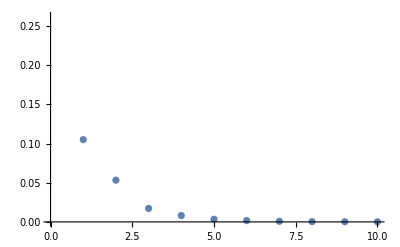

```mathematica
ListPlot[res1]
```

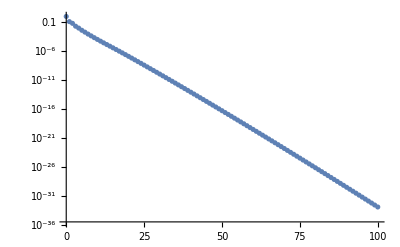

```mathematica
ListLogPlot[res2]
```

### With no specify values

```mathematica
len = 5;
currGenFn = h1[s1,s2,s3,s4,s5];
Clear[j]
```

```mathematica
currGenFn
```

q1^2+2 (1-q1) q1 s1 s2 s5+(1-q1)^2 s1^2 s3 s5^2

```mathematica
For[j=1,j≤len+1,j++,
currGenFn=currGenFn/.{s1->h1[s1,s2,s3,s4,s5],s2->h2[s1,s2,s4,s4,s5],s3->h3[s1,s2,s3,s4],s4->h4[s1,s2,s3,s4],s5->h5[s5]}/.{s3->1,s4->1};]
```

```mathematica
A=Series[currGenFn,{q1,1,2},{α,0,1}]//Expand//Normal
```

1+(-1+q1) (2-2 s5-2 (-1+s5) s5 α)+(-1+q1)^2 (1-8 s5+7 s5^2+2 s5 (4-10 s5+6 s5^2) α)

```mathematica
B=A/.{s1->1,s2->1,s3->1,s4->1}
```

1+(-1+q1) (2-2 s5-2 (-1+s5) s5 α)+(-1+q1)^2 (1-8 s5+7 s5^2+2 s5 (4-10 s5+6 s5^2) α)

```mathematica
res3=Table[{i,Coefficient[B,s5,i]},{i,0,100}]/.{s1->1,s2->1,s3->1,s4->1,s5->0};
```

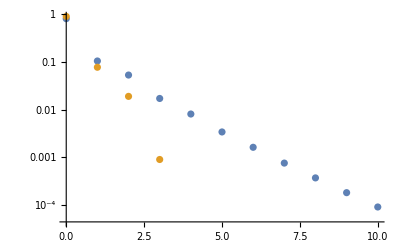

```mathematica
ListLogPlot[{res1,res3/.{q1->0.95,α->0.03}}]
```

### ratio of the change

```mathematica
len = 4;
res=Table[{i,0,0,0},{i,0,len}];
res[[1,2]] = h1[s1,s2,s3,s4,s5];
Clear[j]
```

```mathematica
For[j=2,j≤len+1,j++,
currGenFn =res⟦j-1,2⟧/.{q1->0.9,α->0.2};
currGenFn=currGenFn/.{s1->h1[s1,s2,s4,s4,s5],s1->h2[s1,s2,s4,s4,s5],s3->h3[s1,s2,s4,s4],s4->h4[s1,s2,s4,s4],s5->h5[s5]}/.{q1->0.9,α->0.2};
res⟦j,2⟧=currGenFn/.{q1->0.9,α->0.2};
res⟦j,3⟧=(currGenFn/.{q1->0.9,α->0.2})/res[[j-1,2]];
]
```

```mathematica
res//FullSimplify//TableForm
```

0 | q1^2+2 (1-q1) q1 s1 s2 s5+(1-q1)^2 s1^2 s3 s5^2 | 0 | 0
1 | 0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2 | (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)/(q1^2+2 (1-q1) q1 s1 s2 s5+(1-q1)^2 s1^2 s3 s5^2) | 0
2 | 0.81+0.18 s2 s5 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)+0.01 s5^2 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)^2 | (0.81+0.18 s2 s5 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)+0.01 s5^2 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)^2)/(0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2) | 0
3 | 0.81+0.18 s2 s5 (0.81+0.18 s2 s5 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)+0.01 s5^2 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)^2)+0.01 s5^2 (0.81+0.18 s2 s5 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)+0.01 s5^2 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)^2)^2 | (0.81+0.18 s2 s5 (0.81+0.18 s2 s5 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)+0.01 s5^2 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)^2)+0.01 s5^2 (0.81+0.18 s2 s5 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)+0.01 s5^2 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)^2)^2)/(0.81+0.18 s2 s5 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)+0.01 s5^2 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)^2) | 0
4 | 0.81+0.18 s2 s5 (0.81+0.18 s2 s5 (0.81+0.18 s2 s5 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)+0.01 s5^2 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)^2)+0.01 s5^2 (0.81+0.18 s2 s5 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)+0.01 s5^2 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)^2)^2)+0.01 s5^2 (0.81+0.18 s2 s5 (0.81+0.18 s2 s5 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)+0.01 s5^2 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)^2)+0.01 s5^2 (0.81+0.18 s2 s5 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)+0.01 s5^2 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)^2)^2)^2 | (0.81+0.18 s2 s5 (0.81+0.18 s2 s5 (0.81+0.18 s2 s5 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)+0.01 s5^2 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)^2)+0.01 s5^2 (0.81+0.18 s2 s5 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)+0.01 s5^2 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)^2)^2)+0.01 s5^2 (0.81+0.18 s2 s5 (0.81+0.18 s2 s5 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)+0.01 s5^2 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)^2)+0.01 s5^2 (0.81+0.18 s2 s5 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)+0.01 s5^2 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)^2)^2)^2)/(0.81+0.18 s2 s5 (0.81+0.18 s2 s5 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)+0.01 s5^2 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)^2)+0.01 s5^2 (0.81+0.18 s2 s5 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)+0.01 s5^2 (0.81+0.18 s2 s5 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)+0.01 s5^2 (0.81+0.18 s1 s2 s5+0.01 s1^2 s4 s5^2)^2)^2)^2) | 0

### Mean matrix expected cascade size

### Set up the code

```mathematica
qn[q1_,n_,α_]:=q1 (1-α)^(n-1)
```

```mathematica
pn[q1_,n_,α_]:=1-qn[q1,n,α]
```

```mathematica
p1=pn[q1,1,α]
```

1-q1

```mathematica
p2=pn[q1,2,α]
```

1-q1 (1-α)

```mathematica
Bin[n_,k_,p_]:=PDF[BinomialDistribution[n,p],k]
```

### Mean matrix

```mathematica
m11=FullSimplify[2 ∑_(i=0)^2 i Bin[2,i,p1]]
```

4-4 q1

```mathematica
m12=Expand[FullSimplify[Bin[2,1,p1]]]
```

2 q1-2 q1^2

```mathematica
m13=FullSimplify[Bin[2,2,p1]]
```

(-1+q1)^2

```mathematica
m21=FullSimplify[2 Bin[1,1,p2]]
```

2+2 q1 (-1+α)

```mathematica
m24=FullSimplify[∑_(i=0)^2 i Bin[1,i,p2]]
```

1+q1 (-1+α)

```mathematica
M=({{m11, m12, m13, 0, 1}, {m21, 0, 0, m24, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 1}})
```

{{4-4 q1,2 q1-2 q1^2,(-1+q1)^2,0,1},{2+2 q1 (-1+α),0,0,1+q1 (-1+α),0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,1}}

```mathematica
MatrixForm[M]
```

(4-4 q1 | 2 q1-2 q1^2 | (-1+q1)^2 | 0 | 1
2+2 q1 (-1+α) | 0 | 0 | 1+q1 (-1+α) | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1)

```mathematica
M10=MatrixPower[M/.{q1->0.9,α-> 0.5},100000000]
```

{{0.,0.,0.,0.,2.48756},{0.,0.,0.,0.,2.73632},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,1.}}

```mathematica
M10//MatrixForm
```

(0. | 0. | 0. | 0. | 2.48756
0. | 0. | 0. | 0. | 2.73632
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1.)

```mathematica
z=({{1}, {0}, {0}, {0}, {0}})
```

{{1},{0},{0},{0},{0}}

```mathematica
Transpose[z].M10//MatrixForm
```

(0. | 0. | 0. | 0. | 2.48756)

```mathematica
Eigenvalues[M]
```

{1,0,0,2 (1-q1-√(1-q1-q1^2+q1^3+q1^2 α-q1^3 α)),2 (1-q1+√(1-q1-q1^2+q1^3+q1^2 α-q1^3 α))}

```mathematica
h1[s1,s2,s3,s4,s5]/.{q1->1-p}
```

(1-p)^2+2 (1-p) p s1 s2 s5+p^2 s1^2 s3 s5^2